```mathematica
SetDirectory[NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\shiyin\work\git\work\Critical-region\QCD

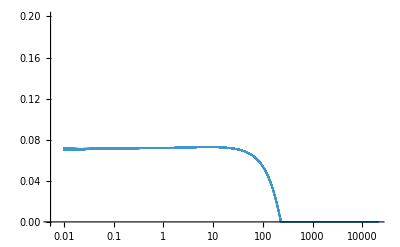

```mathematica
k=Flatten[Import["./v1/BUFFER/K.DAT"]];
rho=Flatten[Import["./v1/BUFFER/RHO.DAT"]];
ListPlot[Transpose[{k,rho[[1;;Length[k]]]/(142.5841442k)}],ScalingFunctions->{"Log",Automatic},PlotRange->{All,{0,0.2}}]
```